```mathematica
(*ClearAll["Global`*"]*)
```

## Assumptions

```mathematica
$Assumptions={};
```

```mathematica
$Assumptions={Element[l,Reals],Element[c,Reals],Element[f,Reals],Z0>0}
```

{l∈ℝ,c∈ℝ,f∈ℝ,True}

## Utility

```mathematica
Conj={Complex[re_,im_]:>Complex[re,-im]};
```

```mathematica
ZPar[zv_]:=FullSimplify[1/Together[Total[1/#&/@zv]]]
```

```mathematica
ZL=2Pi I f l;
ZC=1/(2Pi I f c);
```

## Matching

```mathematica
zpsLC=ZPar[{Z0,ZL}]+ZC;
zpsCL=ZPar[{Z0,ZC}]+ZL;
zspLC=ZPar[{Z0+ZL,ZC}];
zspCL=ZPar[{Z0+ZC,ZL}];
```

```mathematica
ZMatch[netZ_,Z0Data_]:={#[[1]],{netZ/.{f->#[[1]],Z0->#[[2]][[1]]}}}&/@Z0Data
```

```mathematica
Z0RangeFSel[Z0Data_,fmin_,fmax_]:=Select[Z0Data,#[[1]]>fmin && #[[1]]<=fmax&]
```

## Example

```mathematica
Z0ex=sToZ[TSData];
Z0exF=freqAppend[Z0ex];
```

```mathematica
FTuningRange={{0,6 10^8},{0,7 10^8},{7 10^8,8 10^8},{8 10^8,10^9},{10^9,10^10}};
```

```mathematica
Z0exFRange=Z0RangeFSel[Z0exF,#[[1]],#[[2]]]&/@FTuningRange;
```

```mathematica
zpsLCMatched=ZMatch[zpsLC,#]&/@Z0exFRange;
zpsCLMatched=ZMatch[zpsCL,#]&/@Z0exFRange;
zspLCMatched=ZMatch[zspLC,#]&/@Z0exFRange;
zspCLMatched=ZMatch[zspCL,#]&/@Z0exFRange;
```

```mathematica
SpsLCMatched=zToS[#[[;;,2]]]&/@zpsLCMatched
```

```mathematica
Total[(SpsLCMatched[[1]]//Flatten)^2];
```

```mathematica
FindMinimum[Total[(SpsLCMatched[[1]]//Flatten//Abs)^2],{l,10^-12},{c,10^-12}]
```

{40.,{l→1.00037×10^-12,c→5.28258×10^-14}}

```mathematica
SpsLCMatched[[1]]
```

{{(1. (-50.-(0.+3.1831×10^-10 ⅈ)/c+((5.93393×10^9+1.10704×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.×10^8 l)))/(50.-(0.+3.1831×10^-10 ⅈ)/c+((5.93393×10^9+1.10704×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.×10^8 l))},{(1. (-50.-(0.+3.16725×10^-10 ⅈ)/c+((6.19493×10^9+1.19063×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.02503×10^8 l)))/(50.-(0.+3.16725×10^-10 ⅈ)/c+((6.19493×10^9+1.19063×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.02503×10^8 l))},{(1. (-50.-(0.+3.15155×10^-10 ⅈ)/c+((6.45665×10^9+1.27846×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.05005×10^8 l)))/(50.-(0.+3.15155×10^-10 ⅈ)/c+((6.45665×10^9+1.27846×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.05005×10^8 l))},{(1. (-50.-(0.+3.13601×10^-10 ⅈ)/c+((6.74431×10^9+1.36702×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.07508×10^8 l)))/(50.-(0.+3.13601×10^-10 ⅈ)/c+((6.74431×10^9+1.36702×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.07508×10^8 l))},{(1. (-50.-(0.+3.12062×10^-10 ⅈ)/c+((7.06037×10^9+1.45995×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.1001×10^8 l)))/(50.-(0.+3.12062×10^-10 ⅈ)/c+((7.06037×10^9+1.45995×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.1001×10^8 l))},{(1. (-50.-(0.+3.10539×10^-10 ⅈ)/c+((7.40368×10^9+1.55882×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.12513×10^8 l)))/(50.-(0.+3.10539×10^-10 ⅈ)/c+((7.40368×10^9+1.55882×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.12513×10^8 l))},{(1. (-50.-(0.+3.0903×10^-10 ⅈ)/c+((7.81328×10^9+1.65841×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.15015×10^8 l)))/(50.-(0.+3.0903×10^-10 ⅈ)/c+((7.81328×10^9+1.65841×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.15015×10^8 l))},{(1. (-50.-(0.+3.07535×10^-10 ⅈ)/c+((8.24087×10^9+1.75939×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.17518×10^8 l)))/(50.-(0.+3.07535×10^-10 ⅈ)/c+((8.24087×10^9+1.75939×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.17518×10^8 l))},{(1. (-50.-(0.+3.06055×10^-10 ⅈ)/c+((8.6505×10^9+1.86686×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.2002×10^8 l)))/(50.-(0.+3.06055×10^-10 ⅈ)/c+((8.6505×10^9+1.86686×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.2002×10^8 l))},{(1. (-50.-(0.+3.0459×10^-10 ⅈ)/c+((9.12661×10^9+1.97605×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.22523×10^8 l)))/(50.-(0.+3.0459×10^-10 ⅈ)/c+((9.12661×10^9+1.97605×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.22523×10^8 l))},{(1. (-50.-(0.+3.03138×10^-10 ⅈ)/c+((9.61948×10^9+2.09303×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.25025×10^8 l)))/(50.-(0.+3.03138×10^-10 ⅈ)/c+((9.61948×10^9+2.09303×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.25025×10^8 l))},{(1. (-50.-(0.+3.017×10^-10 ⅈ)/c+((1.0119×10^10+2.2167×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.27528×10^8 l)))/(50.-(0.+3.017×10^-10 ⅈ)/c+((1.0119×10^10+2.2167×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.27528×10^8 l))},{(1. (-50.-(0.+3.00275×10^-10 ⅈ)/c+((1.07332×10^10+2.34925×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.3003×10^8 l)))/(50.-(0.+3.00275×10^-10 ⅈ)/c+((1.07332×10^10+2.34925×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.3003×10^8 l))},{(1. (-50.-(0.+2.98864×10^-10 ⅈ)/c+((1.13932×10^10+2.49029×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.32533×10^8 l)))/(50.-(0.+2.98864×10^-10 ⅈ)/c+((1.13932×10^10+2.49029×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.32533×10^8 l))},{(1. (-50.-(0.+2.97466×10^-10 ⅈ)/c+((1.21491×10^10+2.63336×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.35035×10^8 l)))/(50.-(0.+2.97466×10^-10 ⅈ)/c+((1.21491×10^10+2.63336×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.35035×10^8 l))},{(1. (-50.-(0.+2.96082×10^-10 ⅈ)/c+((1.29592×10^10+2.79086×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.37538×10^8 l)))/(50.-(0.+2.96082×10^-10 ⅈ)/c+((1.29592×10^10+2.79086×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.37538×10^8 l))},{(1. (-50.-(0.+2.9471×10^-10 ⅈ)/c+((1.38711×10^10+2.95929×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.4004×10^8 l)))/(50.-(0.+2.9471×10^-10 ⅈ)/c+((1.38711×10^10+2.95929×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.4004×10^8 l))},{(1. (-50.-(0.+2.9335×10^-10 ⅈ)/c+((1.49536×10^10+3.143×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.42543×10^8 l)))/(50.-(0.+2.9335×10^-10 ⅈ)/c+((1.49536×10^10+3.143×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.42543×10^8 l))},{(1. (-50.-(0.+2.92003×10^-10 ⅈ)/c+((1.61686×10^10+3.33421×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.45045×10^8 l)))/(50.-(0.+2.92003×10^-10 ⅈ)/c+((1.61686×10^10+3.33421×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.45045×10^8 l))},{(1. (-50.-(0.+2.90669×10^-10 ⅈ)/c+((1.76673×10^10+3.54047×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.47548×10^8 l)))/(50.-(0.+2.90669×10^-10 ⅈ)/c+((1.76673×10^10+3.54047×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.47548×10^8 l))},{(1. (-50.-(0.+2.89346×10^-10 ⅈ)/c+((1.93133×10^10+3.75034×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.5005×10^8 l)))/(50.-(0.+2.89346×10^-10 ⅈ)/c+((1.93133×10^10+3.75034×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.5005×10^8 l))},{(1. (-50.-(0.+2.88036×10^-10 ⅈ)/c+((2.12373×10^10+3.97085×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.52553×10^8 l)))/(50.-(0.+2.88036×10^-10 ⅈ)/c+((2.12373×10^10+3.97085×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.52553×10^8 l))},{(1. (-50.-(0.+2.86737×10^-10 ⅈ)/c+((2.33982×10^10+4.20252×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.55055×10^8 l)))/(50.-(0.+2.86737×10^-10 ⅈ)/c+((2.33982×10^10+4.20252×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.55055×10^8 l))},{(1. (-50.-(0.+2.8545×10^-10 ⅈ)/c+((2.59836×10^10+4.44571×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.57558×10^8 l)))/(50.-(0.+2.8545×10^-10 ⅈ)/c+((2.59836×10^10+4.44571×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.57558×10^8 l))},{(1. (-50.-(0.+2.84175×10^-10 ⅈ)/c+((2.89721×10^10+4.70318×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.6006×10^8 l)))/(50.-(0.+2.84175×10^-10 ⅈ)/c+((2.89721×10^10+4.70318×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.6006×10^8 l))},{(1. (-50.-(0.+2.82911×10^-10 ⅈ)/c+((3.24522×10^10+4.96778×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.62563×10^8 l)))/(50.-(0.+2.82911×10^-10 ⅈ)/c+((3.24522×10^10+4.96778×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.62563×10^8 l))},{(1. (-50.-(0.+2.81658×10^-10 ⅈ)/c+((3.66703×10^10+5.22263×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.65065×10^8 l)))/(50.-(0.+2.81658×10^-10 ⅈ)/c+((3.66703×10^10+5.22263×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.65065×10^8 l))},{(1. (-50.-(0.+2.80416×10^-10 ⅈ)/c+((4.14522×10^10+5.45599×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.67568×10^8 l)))/(50.-(0.+2.80416×10^-10 ⅈ)/c+((4.14522×10^10+5.45599×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.67568×10^8 l))},{(1. (-50.-(0.+2.79185×10^-10 ⅈ)/c+((4.69084×10^10+5.68526×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.7007×10^8 l)))/(50.-(0.+2.79185×10^-10 ⅈ)/c+((4.69084×10^10+5.68526×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.7007×10^8 l))},{(1. (-50.-(0.+2.77965×10^-10 ⅈ)/c+((5.32995×10^10+5.88065×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.72573×10^8 l)))/(50.-(0.+2.77965×10^-10 ⅈ)/c+((5.32995×10^10+5.88065×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.72573×10^8 l))},{(1. (-50.-(0.+2.76755×10^-10 ⅈ)/c+((6.06188×10^10+6.03347×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.75075×10^8 l)))/(50.-(0.+2.76755×10^-10 ⅈ)/c+((6.06188×10^10+6.03347×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.75075×10^8 l))},{(1. (-50.-(0.+2.75556×10^-10 ⅈ)/c+((6.94467×10^10+6.14535×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.77578×10^8 l)))/(50.-(0.+2.75556×10^-10 ⅈ)/c+((6.94467×10^10+6.14535×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.77578×10^8 l))},{(1. (-50.-(0.+2.74367×10^-10 ⅈ)/c+((7.96915×10^10+6.09372×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.8008×10^8 l)))/(50.-(0.+2.74367×10^-10 ⅈ)/c+((7.96915×10^10+6.09372×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.8008×10^8 l))},{(1. (-50.-(0.+2.73189×10^-10 ⅈ)/c+((9.1353×10^10+5.85157×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.82583×10^8 l)))/(50.-(0.+2.73189×10^-10 ⅈ)/c+((9.1353×10^10+5.85157×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.82583×10^8 l))},{(1. (-50.-(0.+2.7202×10^-10 ⅈ)/c+((1.03981×10^11+5.31573×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.85085×10^8 l)))/(50.-(0.+2.7202×10^-10 ⅈ)/c+((1.03981×10^11+5.31573×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.85085×10^8 l))},{(1. (-50.-(0.+2.70862×10^-10 ⅈ)/c+((1.16358×10^11+4.33943×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.87588×10^8 l)))/(50.-(0.+2.70862×10^-10 ⅈ)/c+((1.16358×10^11+4.33943×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.87588×10^8 l))},{(1. (-50.-(0.+2.69713×10^-10 ⅈ)/c+((1.26613×10^11+2.97568×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.9009×10^8 l)))/(50.-(0.+2.69713×10^-10 ⅈ)/c+((1.26613×10^11+2.97568×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.9009×10^8 l))},{(1. (-50.-(0.+2.68574×10^-10 ⅈ)/c+((1.32724×10^11+1.30903×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.92593×10^8 l)))/(50.-(0.+2.68574×10^-10 ⅈ)/c+((1.32724×10^11+1.30903×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.92593×10^8 l))},{(1. (-50.-(0.+2.67445×10^-10 ⅈ)/c+((1.34679×10^11-4.16904×10^9 ⅈ) l)/((0.-7.95775 ⅈ)+5.95095×10^8 l)))/(50.-(0.+2.67445×10^-10 ⅈ)/c+((1.34679×10^11-4.16904×10^9 ⅈ) l)/((0.-7.95775 ⅈ)+5.95095×10^8 l))},{(1. (-50.-(0.+2.66325×10^-10 ⅈ)/c+((1.32224×10^11-2.13802×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.97598×10^8 l)))/(50.-(0.+2.66325×10^-10 ⅈ)/c+((1.32224×10^11-2.13802×10^10 ⅈ) l)/((0.-7.95775 ⅈ)+5.97598×10^8 l))}}

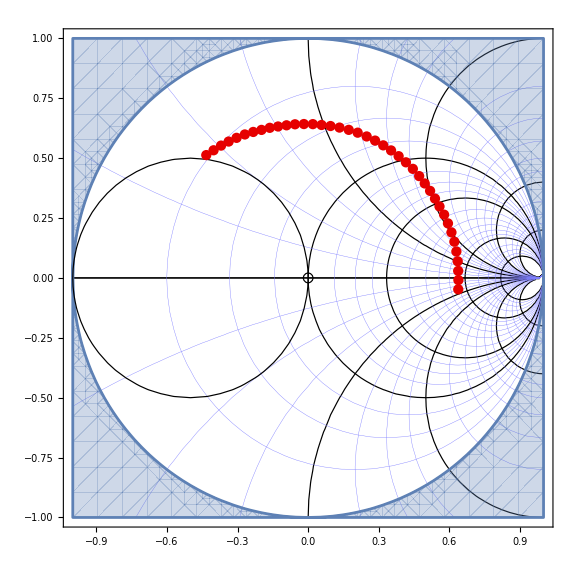

```mathematica
SmithChartListPlot[Z0exFRange[[1,;;,2]]]
```

## asd

```mathematica
Zin=Together[ZPar[{Zl,Zv}]+Zh]
```

(Zh Zl+Zh Zv+Zl Zv)/(Zl+Zv)

```mathematica
ZinSubst=Zin/.{Zv->I Xv,Zh->I Xh,Zl->Rl+I Xl }//FullSimplify
```

-(Xl Xv-ⅈ Rl (Xh+Xv)+Xh (Xl+Xv))/(Rl+ⅈ (Xl+Xv))

```mathematica
ZinSubstRE=ZinSubst//ComplexExpand//Re//FullSimplify
```

-Im[(Rl^2 (Xh+Xv)+(Xl+Xv) (Xh Xl+(Xh+Xl) Xv))/(Rl^2+(Xl+Xv)^2)]+Re[(Rl Xv^2)/(Rl^2+(Xl+Xv)^2)]

```mathematica
ZinSubstIM=ZinSubst//ComplexExpand//Im//FullSimplify
```

Im[(Rl Xv^2)/(Rl^2+(Xl+Xv)^2)]+Re[(Rl^2 (Xh+Xv)+(Xl+Xv) (Xh Xl+(Xh+Xl) Xv))/(Rl^2+(Xl+Xv)^2)]

```mathematica
ZinSubstIMnum=ZinSubstIM//Numerator//ExpandAll//Collect[#,Xh]&
```

Im[(Rl Xv^2)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)]+Re[(Rl^2 Xh)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(Xh Xl^2)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(Rl^2 Xv)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(2 Xh Xl Xv)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(Xl^2 Xv)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(Xh Xv^2)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)+(Xl Xv^2)/(Rl^2+Xl^2+2 Xl Xv+Xv^2)]